#### Init

```mathematica
matall = CloudImport[["https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c"](https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c)];
```

```mathematica
names = Keys[Select[Join@@($LifeParts[#]&/@Keys[$LifeParts]), Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&]];
```

### Highlight uses of object in e.g.: -Graphics-

#### V1

```mathematica
aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]][[-1]]
```

```mathematica
Length[names]
```

979

```mathematica
names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]]
```

{{{0,0,0,0,1,1},{0,0,1,0,1,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,1,0,0},{1,1,0,0,0,0}},{{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1},{0,0,1,0,1,1,0,0},{0,0,1,1,0,1,0,0},{1,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,1,1,0},{0,0,0,1,0,1,1,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,1,1,0,1,0,0,0},{0,1,1,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,1},{0,0,1,0,1,0,0,1},{1,0,0,1,0,1,0,0},{1,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0}}}

```mathematica
frames = 
CellularAutomaton["GameOfLife", {aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]][[-1]], 0}, ]
```

{{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0}}

```mathematica
CausalSeparation[]
```

```mathematica
CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]]]]
```

{{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0},{0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,1,1,1,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0},{0,1,0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,1,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}}

```mathematica
aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]
```

```mathematica
Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]
```

```mathematica
MorphologicalComponents[]
```

```mathematica
Catenate[Position[matall[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20][[9]]]], 1]]
```

{139,169,239,240,262,293,308,324,339,350,352,381,406,408,436,460,461,462,489,490,492,510,522,524,535,536,554,925}

```mathematica
ArrayPlot[SparseArray[#]]&/@
(Thread[#-> 1]&/@

CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

```mathematica
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]][[1]]
]
```

Part::partd: Part specification {15,4}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {15,4}⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{2,2}

```mathematica
ArrayPlot[SparseArray[Thread[(9-  (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
])->1]]]
```

-Graphics-

```mathematica
9 - (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
] === (Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&[
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[4]]]["NonzeroPositions"]][[1]]
]
```

False

```mathematica
((Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#]])&/@
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]]
)
```

{{{5,1},{6,1},{3,2},{5,2},{6,2},{2,3},{5,4},{1,5},{2,5},{4,5},{1,6},{2,6}},{{5,1},{6,1},{7,1},{2,2},{5,2},{6,2},{7,2},{1,3},{3,3},{6,3},{7,3},{2,4}},{{1,1},{2,1},{1,2},{2,2}}}

```mathematica
MemberQ[
SparseArray[#]["NonzeroPositions"]&/@$LifeParts["Oscillator"]["Figure eight"], #
```

{{{1,5},{1,6},{2,3},{2,5},{2,6},{3,2},{4,5},{5,1},{5,2},{5,4},{6,1},{6,2}},{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{5,1},{5,2},{5,3},{6,1},{6,2},{6,3}},{{1,6},{3,4},{3,5},{3,6},{3,8},{4,3},{4,5},{4,6},{5,3},{5,4},{5,6},{6,1},{6,3},{6,4},{6,5},{8,3}},{{1,6},{2,5},{2,7},{3,4},{3,8},{4,3},{4,7},{5,2},{5,6},{6,1},{6,5},{7,2},{7,4},{8,3}},{{1,6},{2,5},{2,6},{2,7},{3,4},{3,6},{3,7},{3,8},{4,3},{4,7},{5,2},{5,6},{6,1},{6,2},{6,3},{6,5},{7,2},{7,3},{7,4},{8,3}},{{1,5},{1,6},{1,7},{2,8},{3,4},{3,8},{4,3},{4,5},{4,8},{5,1},{5,4},{5,6},{6,1},{6,5},{7,1},{8,2},{8,3},{8,4}},{{1,7},{2,7},{2,8},{3,6},{3,7},{3,9},{4,5},{4,8},{4,9},{4,10},{5,4},{5,6},{5,8},{6,3},{6,5},{6,7},{7,1},{7,2},{7,3},{7,6},{8,2},{8,4},{8,5},{9,3},{9,4},{10,4}},{{1,7},{1,8},{3,6},{3,10},{4,5},{4,10},{5,4},{5,6},{5,8},{6,3},{6,5},{6,7},{7,1},{7,6},{8,1},{8,5},{10,3},{10,4}}}

```mathematica
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]]
```

{{{10,7},{10,8},{11,5},{11,7},{11,8},{12,4},{13,7},{14,3},{14,4},{14,6},{15,3},{15,4}},{{4,5},{4,6},{4,7},{5,2},{5,5},{5,6},{5,7},{6,1},{6,3},{6,6},{6,7},{7,2}},{{4,11},{4,12},{5,11},{5,12}}}

```mathematica
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]][[1]]
```

{{10,7},{10,8},{11,5},{11,7},{11,8},{12,4},{13,7},{14,3},{14,4},{14,6},{15,3},{15,4}}

```mathematica
Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]
CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

```mathematica
ArrayPad[SparseArray[
Thread[
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]], {0, 1}]&[]
```

```mathematica
(*ArrayPad[SparseArray[
Thread[
(Transpose[Reverse@{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]], {0, 1}]&/@*)
SparseArray/@(Thread[#-> 1]&/@CausalSeparation[SparseArray[(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]["NonzeroPositions"]])
```

{SparseArray[…],SparseArray[…],SparseArray[…]}

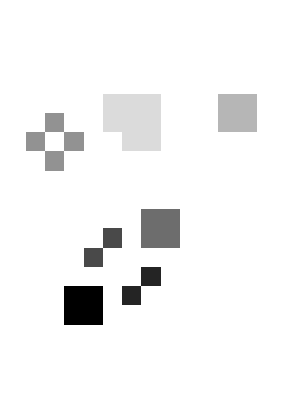

```mathematica
ArrayPlot[MorphologicalComponents@(CellularAutomaton["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[names[[139]]]])[[1]]]
```

#### Dev

```mathematica
Position[names, "Figure eight"]
```

{{169}}

```mathematica
matall[[First@Position[names, "Figure eight"]]]
```

```mathematica
names[[Catenate[Position[matall[[Position[names, "Figure eight"][[1, 1]]]], 1]]]]
```

{Charity's p16,Figure eight,p104lumpsofmuckshuttle,p104rpentominohassler,p120rpentominohassler,p144uturnerhassler,p16centuryhassler,p224 lumps of muck hassler,p280 U-turner hassler,p32 blinker hassler 2,p32 honey farm hassler,p40honeyfarmhassler,p48prepulsarshuttle,p48 toad hassler,p56c2honeyfarmhassler,p64honeyfarmhassler2,p64rpentominohassler2,p64 thunderbird hassler,p72centurylomhassler,p72lumpsofmuckhassler,p72 quasi-shuttle,p80procrastinatorhassler,p88lumpsofmuckhassler2,p88rpentominoshuttle,p96 honey farm hassler,p96honeyfarmhassler2,prepulsarshuttle40,Period-88 glider gun}

```mathematica
matall[[]]
```

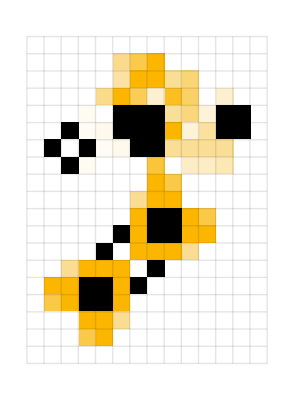
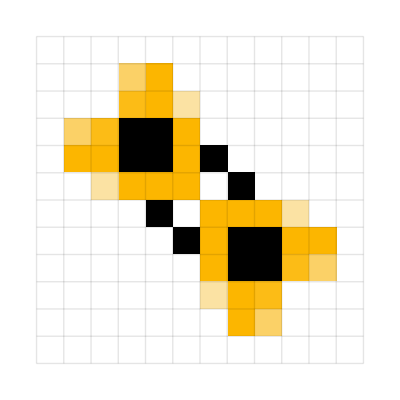
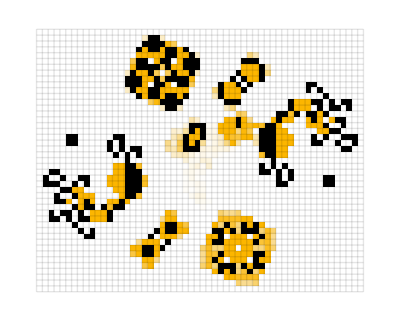
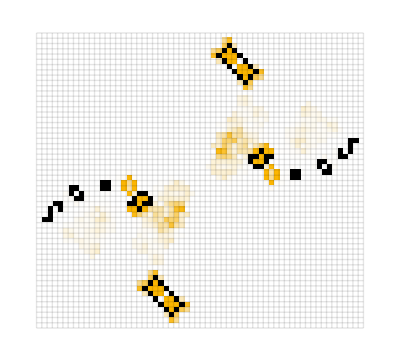
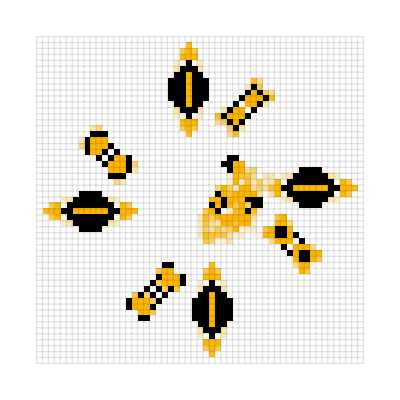
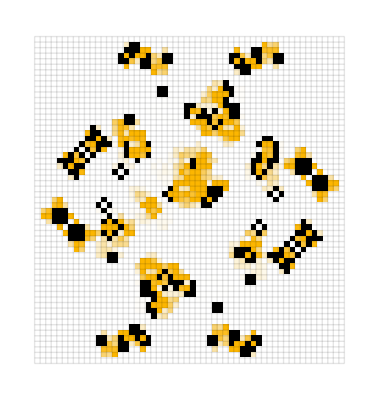
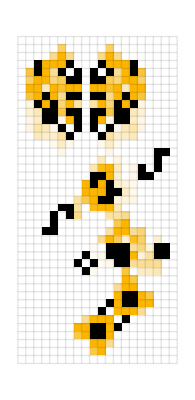
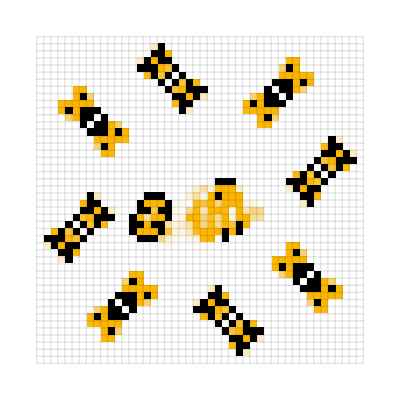

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[#]]&/@names[[Catenate[Position[matall[[Position[names, "Figure eight"][[1, 1]]]], 1]]]]
```

```mathematica
ArrayPlot[SparseArray[Thread[$LifeData["Figure eight", "MatrixData"]["NonzeroPositions"]->1]]]
```

-Graphics-

```mathematica
With[{pos = $LifeData["Figure eight", "MatrixData"]["NonzeroPositions"]},ArrayPlot[Max[pos[[All, 2]]] -SparseArray[Thread[pos->1]]]]
```

-Graphics-

```mathematica
CausalSeparation[pts = $LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]]
```

{{{33,46},{34,46},{34,47},{35,45},{35,46},{35,48},{36,44},{36,47},{36,48},{36,49},{37,43},{37,45},{37,47},{38,42},{38,44},{38,46},{39,40},{39,41},{39,42},{39,45},{40,41},{40,43},{40,44},{41,42},{41,43},{42,43}},{{16,8},{17,8},{17,9},{18,7},{18,8},{18,10},{19,6},{19,9},{19,10},{19,11},{20,5},{20,7},{20,9},{21,4},{21,6},{21,8},{22,2},{22,3},{22,4},{22,7},{23,3},{23,5},{23,6},{24,4},{24,5},{25,5}},{{42,21},{43,20},{43,22},{44,17},{44,18},{44,22},{44,23},{44,24},{44,26},{45,17},{45,18},{45,21},{45,23},{45,26},{46,17},{46,18},{46,19},{46,25},{46,26},{47,19},{48,18},{49,18},{49,19},{50,19}},{{8,32},{9,32},{9,33},{10,33},{11,32},{12,25},{12,26},{12,32},{12,33},{12,34},{13,25},{13,28},{13,30},{13,33},{13,34},{14,25},{14,27},{14,28},{14,29},{14,33},{14,34},{15,29},{15,31},{16,30}},{{31,1},{31,2},{31,3},{32,1},{32,2},{32,3},{33,1},{33,2},{33,3},{34,4},{34,5},{34,6},{35,4},{35,5},{35,6},{36,4},{36,5},{36,6}},{{22,45},{22,46},{22,47},{23,45},{23,46},{23,47},{24,45},{24,46},{24,47},{25,48},{25,49},{25,50},{26,48},{26,49},{26,50},{27,48},{27,49},{27,50}},{{18,39},{18,40},{19,38},{19,41},{20,41},{21,38},{21,41},{22,37},{22,38},{22,40},{22,41},{23,37},{23,40},{24,37},{24,39},{25,38}},{{53,33},{53,34},{54,33},{54,34},{54,37},{54,38},{55,33},{55,36},{55,38},{56,35},{56,36},{56,37},{57,35},{57,36}},{{52,15},{52,16},{53,15},{53,16},{53,17},{54,13},{54,16},{54,18},{55,13},{55,14},{55,17},{55,18},{56,13},{56,14}},{{2,37},{2,38},{3,33},{3,34},{3,37},{3,38},{4,33},{4,35},{4,38},{5,34},{5,35},{5,36},{6,35},{6,36}},{{1,15},{1,16},{2,14},{2,15},{2,16},{3,13},{3,15},{3,18},{4,13},{4,14},{4,17},{4,18},{5,17},{5,18}},{{29,10},{30,9},{30,11},{31,10},{32,11},{33,10},{33,12},{34,13},{35,10},{35,12},{36,11}},{{27,29},{27,30},{27,31},{28,29},{28,30},{28,31},{29,28},{29,30},{30,28},{30,29}},{{19,14},{19,18},{20,14},{21,14},{21,18},{22,16},{23,13},{24,12},{24,14},{25,13}},{{38,34},{38,35},{38,36},{39,34},{39,35},{39,37},{40,36},{40,37}},{{54,29},{54,30},{55,29},{55,30}},{{54,9},{54,10},{55,9},{55,10}},{{48,30},{48,31},{49,30},{49,31}},{{43,36},{43,37},{44,36},{44,37}},{{39,11},{39,12},{40,11},{40,12}},{{33,38},{34,37},{34,39},{35,38}},{{27,41},{28,40},{28,42},{29,41}},{{14,14},{14,15},{15,14},{15,15}},{{9,20},{9,21},{10,20},{10,21}},{{3,41},{3,42},{4,41},{4,42}},{{3,21},{3,22},{4,21},{4,22}},{{27,22},{28,21},{29,22}},{{22,26},{23,26}}}


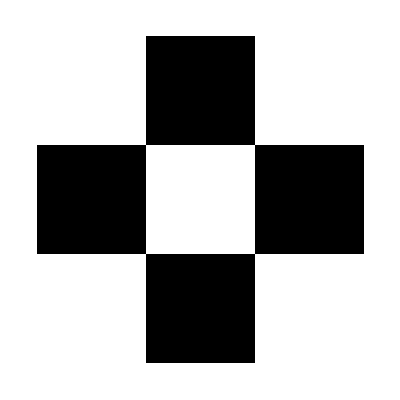
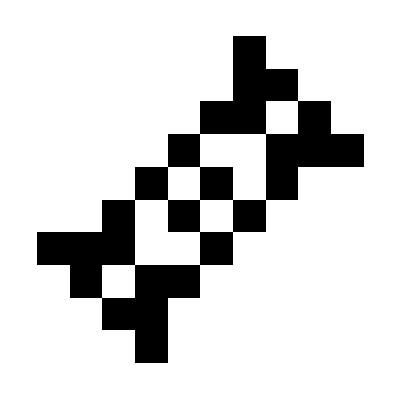
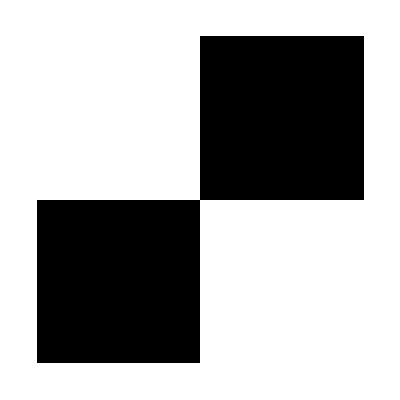
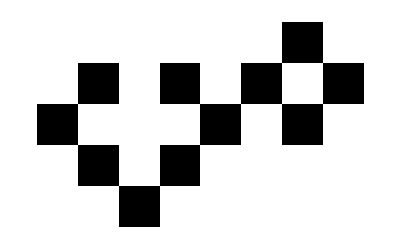
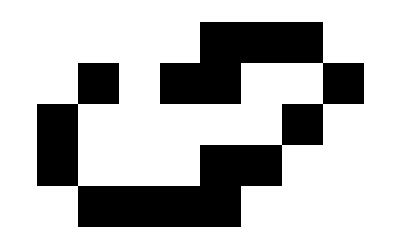
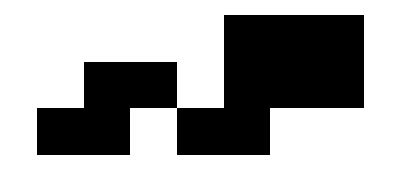
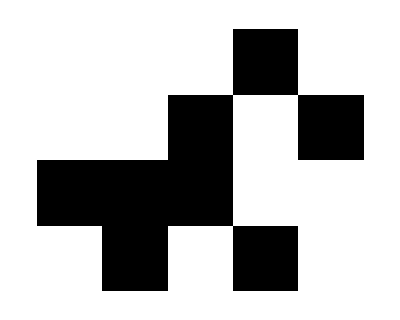
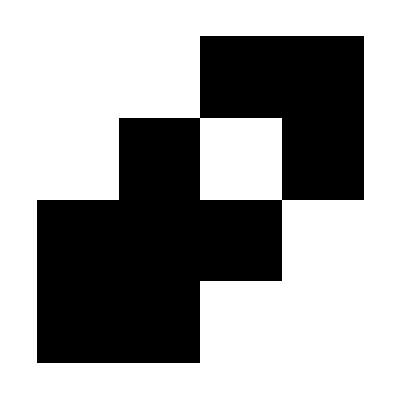
<|-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→1|>

```mathematica
KeyMap[ArrayPlot, PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]
```

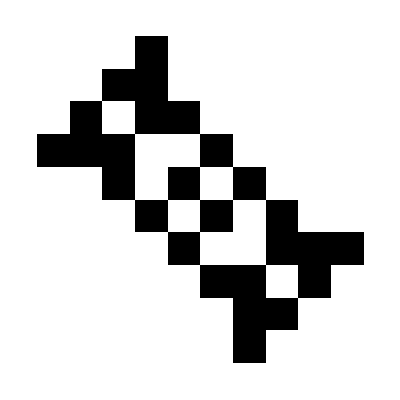
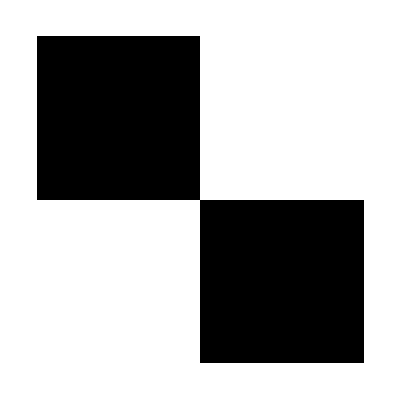
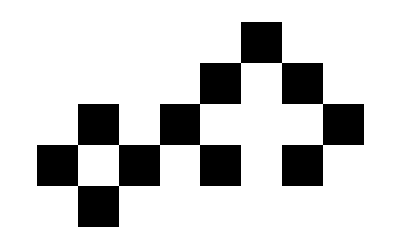
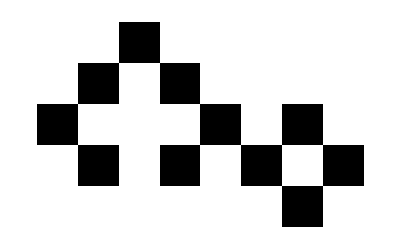
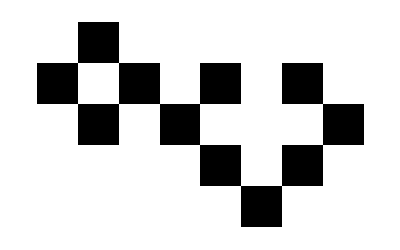
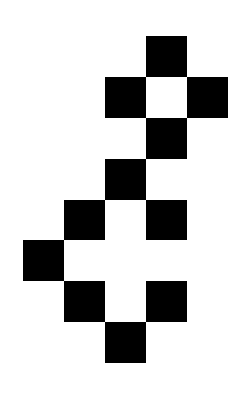
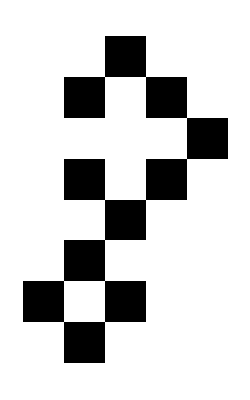
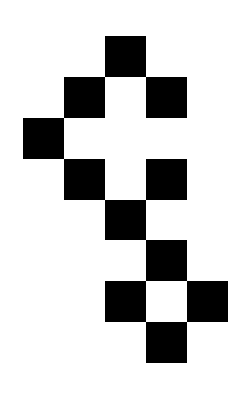
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[ArrayPlot, Sort[ResourceFunction["ArrayRotations"][#]]&/@ Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]], {2}]
```

```mathematica
DeleteDuplicates[Sort[ResourceFunction["ArrayRotations"][#]]&/@ Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]]
```

17

```mathematica
(Sort[ResourceFunction["ArrayRotations"][#]]&/@ Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]])[[1]]
```

{{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}}}

```mathematica
Sort[ResourceFunction["ArrayRotations"][#]]&/@ Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]
```

```mathematica
PatternCanonicalize[$LifeData["Figure eight"]["MatrixData"]]
```

{{1,1,0,0,0,0},{1,1,0,1,0,0},{0,0,0,0,1,0},{0,1,0,0,0,0},{0,0,1,0,1,1},{0,0,0,0,1,1}}

```mathematica
PatternCanonicalize[Transpose[$LifeData["Figure eight"]["MatrixData"]]]
```

{{1,1,0,0,0,0},{1,1,0,1,0,0},{0,0,0,0,1,0},{0,1,0,0,0,0},{0,0,1,0,1,1},{0,0,0,0,1,1}}

```mathematica
ArrayPlot@PatternCanonicalize[$LifeData["Figure eight"]["MatrixData"]]
```

-Graphics-

```mathematica
Pattern
```

```mathematica
Map[ArrayPlot[PatternCanonicalize2[#]]&, Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, #Period}]&[$LifeData["Figure eight"]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PatternCanonicalize[]
```

```mathematica
ArrayPlot/@PatternCanonicalize2/@Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PatternCanonicalize2/@Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]
```

```mathematica
ArrayPlot/@Intersection[PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, #Period - 1}]&[$LifeData["Figure eight"]], PatternCanonicalize2/@Keys[PatternElements[$LifeData["p144uturnerhassler", "MatrixData"]]]]
```

{-Graphics-,-Graphics-}

```mathematica
Position[{{1, 2, 3}, {4, 5, 6}}, {2, 3}]
```

{}

```mathematica
Position[{{1, 2, 3}, {4, 5, 6}}, {1, 2, 3}]
```

{{1}}

```mathematica
Intersection[]
```

```mathematica
(*$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"] *)ArrayPlot[SparseArray[Thread[#->1]]]&/@CausalSeparation[$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]
```

{{1,15},{1,16},{2,14},{2,15},{2,16},{2,37},{2,38},{3,13},{3,15},{3,18},{3,21},{3,22},{3,33},{3,34},{3,37},{3,38},{3,41},{3,42},{4,13},{4,14},{4,17},{4,18},{4,21},{4,22},{4,33},{4,35},{4,38},{4,41},{4,42},{5,17},{5,18},{5,34},{5,35},{5,36},{6,35},{6,36},{8,32},{9,20},{9,21},{9,32},{9,33},{10,20},{10,21},{10,33},{11,32},{12,25},{12,26},{12,32},{12,33},{12,34},{13,25},{13,28},{13,30},{13,33},{13,34},{14,14},{14,15},{14,25},{14,27},{14,28},{14,29},{14,33},{14,34},{15,14},{15,15},{15,29},{15,31},{16,8},{16,30},{17,8},{17,9},{18,7},{18,8},{18,10},{18,39},{18,40},{19,6},{19,9},{19,10},{19,11},{19,14},{19,18},{19,38},{19,41},{20,5},{20,7},{20,9},{20,14},{20,41},{21,4},{21,6},{21,8},{21,14},{21,18},{21,38},{21,41},{22,2},{22,3},{22,4},{22,7},{22,16},{22,26},{22,37},{22,38},{22,40},{22,41},{22,45},{22,46},{22,47},{23,3},{23,5},{23,6},{23,13},{23,26},{23,37},{23,40},{23,45},{23,46},{23,47},{24,4},{24,5},{24,12},{24,14},{24,37},{24,39},{24,45},{24,46},{24,47},{25,5},{25,13},{25,38},{25,48},{25,49},{25,50},{26,48},{26,49},{26,50},{27,22},{27,29},{27,30},{27,31},{27,41},{27,48},{27,49},{27,50},{28,21},{28,29},{28,30},{28,31},{28,40},{28,42},{29,10},{29,22},{29,28},{29,30},{29,41},{30,9},{30,11},{30,28},{30,29},{31,1},{31,2},{31,3},{31,10},{32,1},{32,2},{32,3},{32,11},{33,1},{33,2},{33,3},{33,10},{33,12},{33,38},{33,46},{34,4},{34,5},{34,6},{34,13},{34,37},{34,39},{34,46},{34,47},{35,4},{35,5},{35,6},{35,10},{35,12},{35,38},{35,45},{35,46},{35,48},{36,4},{36,5},{36,6},{36,11},{36,44},{36,47},{36,48},{36,49},{37,43},{37,45},{37,47},{38,34},{38,35},{38,36},{38,42},{38,44},{38,46},{39,11},{39,12},{39,34},{39,35},{39,37},{39,40},{39,41},{39,42},{39,45},{40,11},{40,12},{40,36},{40,37},{40,41},{40,43},{40,44},{41,42},{41,43},{42,21},{42,43},{43,20},{43,22},{43,36},{43,37},{44,17},{44,18},{44,22},{44,23},{44,24},{44,26},{44,36},{44,37},{45,17},{45,18},{45,21},{45,23},{45,26},{46,17},{46,18},{46,19},{46,25},{46,26},{47,19},{48,18},{48,30},{48,31},{49,18},{49,19},{49,30},{49,31},{50,19},{52,15},{52,16},{53,15},{53,16},{53,17},{53,33},{53,34},{54,9},{54,10},{54,13},{54,16},{54,18},{54,29},{54,30},{54,33},{54,34},{54,37},{54,38},{55,9},{55,10},{55,13},{55,14},{55,17},{55,18},{55,29},{55,30},{55,33},{55,36},{55,38},{56,13},{56,14},{56,35},{56,36},{56,37},{57,35},{57,36}}

```mathematica
CausalSeparation[$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]]
```

{{{33,46},{34,46},{34,47},{35,45},{35,46},{35,48},{36,44},{36,47},{36,48},{36,49},{37,43},{37,45},{37,47},{38,42},{38,44},{38,46},{39,40},{39,41},{39,42},{39,45},{40,41},{40,43},{40,44},{41,42},{41,43},{42,43}},{{16,8},{17,8},{17,9},{18,7},{18,8},{18,10},{19,6},{19,9},{19,10},{19,11},{20,5},{20,7},{20,9},{21,4},{21,6},{21,8},{22,2},{22,3},{22,4},{22,7},{23,3},{23,5},{23,6},{24,4},{24,5},{25,5}},{{42,21},{43,20},{43,22},{44,17},{44,18},{44,22},{44,23},{44,24},{44,26},{45,17},{45,18},{45,21},{45,23},{45,26},{46,17},{46,18},{46,19},{46,25},{46,26},{47,19},{48,18},{49,18},{49,19},{50,19}},{{8,32},{9,32},{9,33},{10,33},{11,32},{12,25},{12,26},{12,32},{12,33},{12,34},{13,25},{13,28},{13,30},{13,33},{13,34},{14,25},{14,27},{14,28},{14,29},{14,33},{14,34},{15,29},{15,31},{16,30}},{{31,1},{31,2},{31,3},{32,1},{32,2},{32,3},{33,1},{33,2},{33,3},{34,4},{34,5},{34,6},{35,4},{35,5},{35,6},{36,4},{36,5},{36,6}},{{22,45},{22,46},{22,47},{23,45},{23,46},{23,47},{24,45},{24,46},{24,47},{25,48},{25,49},{25,50},{26,48},{26,49},{26,50},{27,48},{27,49},{27,50}},{{18,39},{18,40},{19,38},{19,41},{20,41},{21,38},{21,41},{22,37},{22,38},{22,40},{22,41},{23,37},{23,40},{24,37},{24,39},{25,38}},{{53,33},{53,34},{54,33},{54,34},{54,37},{54,38},{55,33},{55,36},{55,38},{56,35},{56,36},{56,37},{57,35},{57,36}},{{52,15},{52,16},{53,15},{53,16},{53,17},{54,13},{54,16},{54,18},{55,13},{55,14},{55,17},{55,18},{56,13},{56,14}},{{2,37},{2,38},{3,33},{3,34},{3,37},{3,38},{4,33},{4,35},{4,38},{5,34},{5,35},{5,36},{6,35},{6,36}},{{1,15},{1,16},{2,14},{2,15},{2,16},{3,13},{3,15},{3,18},{4,13},{4,14},{4,17},{4,18},{5,17},{5,18}},{{29,10},{30,9},{30,11},{31,10},{32,11},{33,10},{33,12},{34,13},{35,10},{35,12},{36,11}},{{27,29},{27,30},{27,31},{28,29},{28,30},{28,31},{29,28},{29,30},{30,28},{30,29}},{{19,14},{19,18},{20,14},{21,14},{21,18},{22,16},{23,13},{24,12},{24,14},{25,13}},{{38,34},{38,35},{38,36},{39,34},{39,35},{39,37},{40,36},{40,37}},{{54,29},{54,30},{55,29},{55,30}},{{54,9},{54,10},{55,9},{55,10}},{{48,30},{48,31},{49,30},{49,31}},{{43,36},{43,37},{44,36},{44,37}},{{39,11},{39,12},{40,11},{40,12}},{{33,38},{34,37},{34,39},{35,38}},{{27,41},{28,40},{28,42},{29,41}},{{14,14},{14,15},{15,14},{15,15}},{{9,20},{9,21},{10,20},{10,21}},{{3,41},{3,42},{4,41},{4,42}},{{3,21},{3,22},{4,21},{4,22}},{{27,22},{28,21},{29,22}},{{22,26},{23,26}}}

```mathematica
Module[{},subidxs = CausalSeparation[$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]];
tofind = PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, #Period - 1}]&[$LifeData["Figure eight"]];
torep = Select[subidxs, MemberQ[tofind, PatternCanonicalize2[Normal[SparseArray[Thread[#->1]]]]]&];
subs = PatternCanonicalize2[Normal[SparseArray[Thread[#->1]]]]&/@subidxs;
ArrayPlot[ReplacePart[$LifeData["p144uturnerhassler", "MatrixData"], Thread[torep->Red]]]]
```

-Graphics-

```mathematica
ArrayPlot/@tofind
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@subs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
intersectingidxs[pat_, subpats_]:=  
Select[
CausalSeparation[
$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]
], MemberQ[subpats, 
PatternCanonicalize2[ResourceFunction["ArrayCrop"][Normal[SparseArray[Thread[#->1]]]]]]&]
```

```mathematica
(ArrayPlot[PatternCanonicalize2[ResourceFunction["ArrayCrop"][Normal[SparseArray[Thread[#->1]]]]]]&/@WeaklyConnectedComponents[
NearestNeighborGraph[#,
{All,2Sqrt[2]}]]&[
$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]
])[[{5, 6}]]
```

{-Graphics-,-Graphics-}

```mathematica
ArrayPlot[ReplacePart[$LifeData["p144uturnerhassler", "MatrixData"], 
Thread[
Select[
CausalSeparation[
SparseArray[$LifeData["p144uturnerhassler", "MatrixData"]]["NonzeroPositions"]
], MemberQ[PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, #Period - 1}]&[$LifeData["Figure eight"]], PatternCanonicalize2[ResourceFunction["ArrayCrop"][Normal[SparseArray[Thread[#->1]]]]]]&]->Red]]]
```

-Graphics-

```mathematica
PatternCanonicalize2[SparseArray[Thread[#->1]]]&/@CausalSeparation[$LifeData["p144uturnerhassler", "MatrixData"]["NonzeroPositions"]]
```

{{{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,1,1,1,0,0},{0,1,1,0,1,1,1,0,0},{1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,1,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,1,1,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,1,1},{1,1,0,0,1,0,1,0,0,1},{1,1,0,0,0,1,1,1,0,1},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}},{{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0},{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1}},{{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}},{{0,1,1,0,0},{1,0,0,1,0},{1,0,0,0,0},{1,0,0,1,0},{1,1,0,1,1},{0,1,0,0,1},{0,0,1,0,1},{0,0,0,1,0}},{{0,0,1,1,1},{0,0,0,1,1},{1,1,0,0,0},{1,1,1,0,0},{0,1,0,1,0},{0,0,1,1,0}},{{1,1,1,0,0},{1,1,0,0,0},{0,0,0,1,1},{0,0,1,1,1},{0,1,0,1,0},{0,1,1,0,0}},{{1,1,0,0,0,0},{1,1,0,0,1,1},{1,0,0,1,0,1},{0,0,1,1,1,0},{0,0,1,1,0,0}},{{0,0,1,1,0,0},{0,0,1,1,1,0},{1,0,0,1,0,1},{1,1,0,0,1,1},{1,1,0,0,0,0}},{{0,0,0,0,0,0,1,0},{0,1,0,1,0,1,0,1},{1,0,0,0,1,0,1,0},{0,1,0,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{1,1,1,0},{1,1,1,0},{0,1,0,1},{0,0,1,1}},{{0,1,0,0,0,0,0},{1,0,1,0,0,0,0},{0,1,0,0,1,1,1},{0,0,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,1,0,1}},{{0,1,1},{0,1,1},{1,0,1},{1,1,0}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{0,1,0},{1,0,1},{0,1,0}},{{0,1,0},{1,0,1},{0,1,0}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{0,1,0},{1,0,1}},{{1},{1}}}

#### Running

```mathematica
intersectingidxs[pat_, subpats_]:=  
Select[
CausalSeparation[
SparseArray[pat]["NonzeroPositions"]
], MemberQ[subpats, 
PatternCanonicalize2[ResourceFunction["ArrayCrop"][Normal[SparseArray[Thread[#->1]]]]]]&]
```

```mathematica
With[{pat = $LifeData["p144uturnerhassler", "MatrixData"]},
 ArrayPlot[ReplacePart[pat, 
Thread[#->Red]]]&[
intersectingidxs[pat, #]&[
PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, #Period - 1}]&[$LifeData["Figure eight"]]
]
]]
```

-Graphics-

```mathematica
GraphicsGrid[Function[name, With[{pat = $LifeData[#, "MatrixData"]},
 ArrayPlot[ReplacePart[pat, 
Thread[#->Red]], ImageSize->50]&[
intersectingidxs[pat, #]&[
PatternCanonicalize2/@Table[CellularAutomaton["GameOfLife", {#MatrixData, 0},{{{i}}}], {i, 0, Replace[#[["Period"]],_Missing->1] - 1}]&[$LifeData[name]]
]
]]&/@Take[names[[Catenate[Position[matall[[Position[names, name][[1, 1]]]], 1]]]], UpTo[10]]]/@byrank[[;;5]]]
```

```mathematica
byrank = names[[ReverseSortBy[Range[Length[matall]], Total[matall[[#]]]&]]];
```

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0},Replace[#[["Period"]],_Missing->1] - 1]&[$LifeData[#]]&/@byrank[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Checking out weirdo

```mathematica
byrank[[4]]
```

Three-block shifter

```mathematica
$LifeParts["Oscillator", "Three-block shifter"]
```

Missing[KeyAbsent,Three-block shifter]

```mathematica
Keys[$LifeParts]
```

{Oscillator,Spaceship,Strict still life,Gun,Puffer,Induction coil,Reflector}

```mathematica
ArrayPlot/@$LifeParts["Reflector",  "Three-block shifter"]
```

{-Graphics-,-Graphics-,-Graphics-}

### Attempting to recompute more accurate lifeparts

#### V1

```mathematica
alllayers = Select[$LifeData, Times@@Dimensions[#MatrixData]<
```

1393

```mathematica
Histogram[(Times@@Dimensions[#MatrixData]&/@ Values[$LifeData])[[;;500]]]
```

-Graphics-

```mathematica
Histogram[Values[Times@@Dimensions[#MatrixData]&/@ $LifeData],{1}, PlotRange->{{0, 10000}, Automatic}]
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
Histogram[Times@@Dimensions[#MatrixData]&/@ $LifeData, {1}]
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
$LifeData["Pole 2"]
```

<|Name→Pole 2,Year→1970,Class→Rotor,Wiki→https://conwaylife.com/wiki/Pole_2,DataFiles→{pole2rotor.cells,pole2rotor.rle},MatrixData→SparseArray[Automatic,{1,3},0,{1,{{0,2},{{1},{3}}},{47,47}}],InitialWeight→94|>

```mathematica
small = Select[$LifeData, Times@@Dimensions[#MatrixData]<2000&& Replace[#[["Period"]],_Missing->1]<=350&];
```

```mathematica
layers = ParallelMap[CausalSeparation[SparseArray[#]["NonzeroPositions"]]&/@CellularAutomaton["GameOfLife", {#MatrixData, 0}, Replace[#[["Period"]],_Missing->1] - 1]&, small];
```

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

NearestNeighborGraph::list: List expected at position 1 in ….

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

NearestNeighborGraph::list: List expected at position 1 in ….

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in SparseArray[0].

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

SparseArray::list: List expected at position 1 in SparseArray[0].

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

NearestNeighborGraph::list: List expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

SparseArray::list: List expected at position 1 in SparseArray[0].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

SparseArray::list: List expected at position 1 in SparseArray[0].

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]]].

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

General::stop: Further output of SparseArray::rect will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

General::stop: Further output of CellularAutomaton::nspecnl will be suppressed during this calculation.

```mathematica
worked = layers[[Catenate[Position[layers, _List, {1}, Heads-> False]]]];
```

```mathematica
$LifeData["Block", "MatrixData"]
```

```mathematica
Select[layers, 
MemberQ[DeleteDuplicates[
PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@Flatten[#, 2]]&, $Life]
```

SparseArray[…]

```mathematica
PatternCanonicalize[Normal[$LifeData["Block", "MatrixData"]]]
```

{{1,1},{1,1}}

```mathematica
$LifeData["Block", "MatrixData"]["Density"]
```

1.

```mathematica
$LifeData["Block", "MatrixData"]
```

Keys::invrl: The argument … is not a valid Association or a list of rules.

Keys[SparseArray[…]]

```mathematica
Flatten[{{{1, 2, 3}}}, 2]
```

{1,2,3}

```mathematica
Position[Values[layers], Except[_List]]
```

$Aborted

```mathematica
Keys[layers][[Catenate[p]]]
```

{List,Pole 2,Flutter,Unique father problem}

```mathematica
ArrayPlot[$LifeData[#, "MatrixData"]]&/@Keys[layers][[Catenate[p]]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
p = Position[Values[layers], Except[_List], {1}, Heads->False];
```

```mathematica
p
```

{{56},{88},{838}}

```mathematica
small[[{56}]]
```

<|Pole 2→<|Name→Pole 2,Year→1970,Class→Rotor,Wiki→https://conwaylife.com/wiki/Pole_2,DataFiles→{pole2rotor.cells,pole2rotor.rle},MatrixData→SparseArray[Automatic,{1,3},0,{1,{{0,2},{{1},{3}}},{47,47}}],InitialWeight→94|>|>

```mathematica
CellularAutomaton["GameOfLife",{#MatrixData, 0}, Replace[#[["Period"]],_Missing->1] - 1]&[#]&/@ small[[;;100]]
```

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

```mathematica
layers[[2]]
```

{{{{2,1},{2,2},{2,3}}},{{{1,2},{2,2},{3,2}}}}

```mathematica
Select[$LifeData, #MatrixData ===SparseArray[…]&]
```

<|Pole 2→<|Name→Pole 2,Year→1970,Class→Rotor,Wiki→https://conwaylife.com/wiki/Pole_2,DataFiles→{pole2rotor.cells,pole2rotor.rle},MatrixData→SparseArray[Automatic,{1,3},0,{1,{{0,2},{{1},{3}}},{47,47}}],InitialWeight→94|>|>

```mathematica
$LifeData["Pole 2"]["MatrixData"] // Normal
```

{{47,0,47}}

```mathematica
Map[ArrayPlot[SparseArray[Thread[#-> 1]]]&,#, {2}]&/@ layers
```

<|HF95P→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},p6 pipsquirter→{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},Period-24 glider gun→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},Period-44 glider gun→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},PF35W→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},RF48H→{{-Graphics-,-Graphics-,-Graphics-}},Rx202→{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},Spider→{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},Waveguide 1→{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},28P7.1→{{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}},28P7.2→{{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}|>

```mathematica
Thread[#-> 1]&/@ layers[[1]]
```

{{{{1,2},{1,3},{2,1},{2,4},{3,2},{3,3}}→1}}

```mathematica
Histogram[Values[Replace[#[["Period"]],_Missing->1]&/@ $LifeData]]
```

-Graphics-

#### V2

```mathematica
small = Select[$LifeData, Times@@Dimensions[#MatrixData]<2000&& Replace[#[["Period"]],_Missing->1]<=350&];
```

```mathematica
(*layers = ParallelMap[CausalSeparation[SparseArray[#]["NonzeroPositions"]]&/@CellularAutomaton["GameOfLife", {#MatrixData, 0}, Replace[#[["Period"]],_Missing->1] - 1]&, small] // Quiet;*)
```

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

NearestNeighborGraph::list: List expected at position 1 in ….

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

NearestNeighborGraph::list: List expected at position 1 in ….

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in SparseArray[0].

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

SparseArray::list: List expected at position 1 in SparseArray[0].

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

CellularAutomaton::initn: The initial condition specification … should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

SparseArray::list: List expected at position 1 in SparseArray[GameOfLife].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}].

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[SparseArray[GameOfLife][NonzeroPositions],{All,2 √2}]].

NearestNeighborGraph::inv: The argument SparseArray[GameOfLife][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]] is not a valid specification.

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]].

SparseArray::rect: List of rules or non-empty rectangular array expected at position 1 in ….

NearestNeighborGraph::list: List expected at position 1 in ….

WeaklyConnectedComponents::graph: A graph object is expected at position 1 in ….

General::stop: Further output of WeaklyConnectedComponents::graph will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument … in … is not a valid specification.

SparseArray::list: List expected at position 1 in SparseArray[0].

NearestNeighborGraph::list: List expected at position 1 in NearestNeighborGraph[SparseArray[0][NonzeroPositions],{All,2 √2}].

General::stop: Further output of NearestNeighborGraph::list will be suppressed during this calculation.

NearestNeighborGraph::inv: The argument SparseArray[0][NonzeroPositions] in NearestNeighborGraph[{All,2 √2},SparseArray[0][NonzeroPositions]] is not a valid specification.

General::stop: Further output of NearestNeighborGraph::inv will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification WeaklyConnectedComponents[NearestNeighborGraph[{All,2 √2},SparseArray[GameOfLife][NonzeroPositions]]] should be an Integer, a List, a pure Boolean function, a String or an Association.

```mathematica
layers = Import["https://www.wolframcloud.com/obj/sw-writings/$PartIndexes"];
```

```mathematica
worked = layers[[Catenate[Position[layers, _List, {1}, Heads-> False]]]];
```

```mathematica
b = ParallelSelect[worked, 
MemberQ[DeleteDuplicates[
PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@Catenate[#]], Normal[$LifeData["Block", "MatrixData"]]]&];
```

```mathematica
Iconize[Keys[b]]
```

```mathematica
ArrayPlot/@DeleteDuplicates[
PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@Flatten[#, 2]]&/@ worked[[;;1]]
```

ArrayPlot::mat: Argument {1,1} at position 1 is not a list of lists.

ArrayPlot::mat: Argument {1,0,1} at position 1 is not a list of lists.

ArrayPlot::mat: Argument {1} at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

<|Beehive→{ArrayPlot[{1,1}],ArrayPlot[{1,0,1}],ArrayPlot[{1}]}|>

```mathematica
worked[[;;1]]
```

<|Beehive→{{{{1,2},{1,3},{2,1},{2,4},{3,2},{3,3}}}}|>

```mathematica
Catenate[#]&/@ worked[[;;1]]
```

<|Beehive→{{{1,2},{1,3},{2,1},{2,4},{3,2},{3,3}}}|>

```mathematica
DeleteDuplicates[
PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@Catenate[#]]&/@ worked[[;;10]]
```

<|Beehive→{{{0,1,1,0},{1,0,0,1},{0,1,1,0}}},Blinker→{{{1,1,1}}},Block→{{{1,1},{1,1}}},Crotchet→{{{0,1,1},{1,1,1}}},Domino→{{{1,1}}},Dot→{{{1}}},Duoplet→{{{0,1},{1,0}}},Glider→{{{0,0,1},{1,0,1},{0,1,1}},{{0,0,1},{1,1,0},{0,1,1}}},Line of three→{{{1,1,1}}},Loaf→{{{0,0,1,0},{0,1,0,1},{1,0,0,1},{0,1,1,0}}}|>

```mathematica
allarrays = ParallelMap[DeleteDuplicates[
PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@Catenate[#]]&, worked];
```

$Aborted

### Trying to make recompute faster

#### Dev1

```mathematica
TakeLargest[Reverse@{{1, 3}, {2, 4}}, 1]
```

{{2,4}}

```mathematica
worked[[800, 1]]
```

{{{2,9},{3,4},{3,5},{3,10},{3,11},{4,2},{4,3},{4,4},{4,6},{4,7},{4,10},{4,11},{5,1},{5,10},{6,2},{6,4},{6,5},{7,2},{7,4},{7,8},{7,10},{8,7},{8,8},{8,10},{9,2},{9,11},{10,1},{10,2},{10,5},{10,6},{10,8},{10,9},{10,10},{11,1},{11,2},{11,7},{11,8},{12,3}}}

```mathematica
LocalizePoints/@worked[[500, 1]]
```

{{{1,24},{1,27},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{3,18},{3,19},{3,21},{3,30},{4,14},{4,15},{4,17},{4,19},{4,21},{4,23},{4,24},{4,25},{4,26},{4,27},{4,28},{4,29},{4,30},{4,33},{5,12},{5,13},{5,14},{5,16},{5,17},{5,21},{5,23},{5,31},{5,32},{5,33},{6,11},{6,16},{6,17},{6,18},{6,21},{6,25},{6,29},{6,30},{7,12},{7,13},{7,14},{7,18},{7,19},{7,21},{7,22},{7,23},{7,24},{7,26},{7,30},{7,32},{7,33},{8,13},{8,15},{8,19},{8,25},{8,30},{8,33},{9,11},{9,20},{9,22},{9,23},{9,26},{9,27},{9,30},{9,31},{10,11},{10,12},{10,13},{10,14},{10,15},{10,17},{10,18},{10,19},{10,20},{10,22},{10,27},{10,28},{10,29},{11,16},{11,17},{11,22},{11,27},{11,29},{11,30},{11,31},{12,13},{12,14},{12,15},{12,16},{12,17},{12,19},{12,20},{12,21},{12,26},{12,27},{12,29},{12,30},{13,12},{13,18},{13,19},{13,24},{13,25},{13,27},{13,29},{13,30},{14,13},{14,14},{14,15},{14,16},{14,17},{14,24},{14,25},{14,27},{14,31},{15,1},{15,2},{15,4},{15,5},{15,15},{15,16},{15,19},{15,25},{15,27},{15,32},{16,2},{16,4},{16,6},{16,8},{16,10},{16,11},{16,15},{16,16},{16,17},{16,19},{16,26},{16,29},{16,31},{17,1},{17,4},{17,12},{17,19},{17,20},{17,24},{17,25},{17,26},{18,1},{18,2},{18,3},{18,6},{18,11},{18,12},{18,24},{19,6},{19,7},{19,8},{19,9},{19,11},{20,3},{20,4},{20,6},{20,13},{21,2},{21,7},{21,11},{22,2},{22,3},{22,4},{22,6},{22,11},{23,12},{24,2},{24,3},{24,4},{24,6},{24,11},{25,2},{25,7},{25,11},{26,3},{26,4},{26,6},{26,13},{27,6},{27,7},{27,8},{27,9},{27,11},{28,1},{28,2},{28,3},{28,6},{28,11},{28,12},{29,1},{29,4},{29,12},{30,2},{30,4},{30,6},{30,8},{30,10},{30,11},{31,1},{31,2},{31,4},{31,5}},{{1,9},{1,10},{1,12},{2,8},{2,10},{2,11},{2,13},{3,8},{3,13},{4,5},{4,6},{4,8},{4,10},{4,11},{4,13},{4,14},{5,5},{5,7},{5,9},{5,11},{5,13},{6,7},{6,13},{7,6},{7,8},{7,10},{7,11},{7,13},{7,14},{8,6},{8,7},{8,8},{8,10},{8,12},{9,7},{9,8},{9,9},{9,12},{10,6},{10,8},{10,10},{10,11},{11,6},{12,6},{12,7},{13,6},{13,7},{14,6},{14,7},{15,6},{16,6},{16,8},{16,10},{16,11},{17,7},{17,8},{17,9},{17,12},{18,6},{18,7},{18,8},{18,10},{18,12},{19,6},{19,8},{19,10},{19,11},{19,13},{19,14},{20,7},{20,13},{21,5},{21,7},{21,9},{21,11},{21,13},{22,5},{22,6},{22,8},{22,10},{22,11},{22,13},{22,14},{23,2},{23,8},{23,13},{24,3},{24,8},{24,10},{24,11},{24,13},{25,1},{25,2},{25,3},{25,9},{25,10},{25,12}},{{1,2},{1,3},{2,1},{2,5},{3,1},{4,1},{4,5},{5,2},{5,3}},{{1,1},{1,2},{2,1},{3,2},{3,3},{3,4},{4,4}},{{1,2},{2,3},{3,1},{3,2},{3,3}},{{1,1},{2,2},{2,3},{3,1}},{{1,1}}}

```mathematica
LocalizePoints[#]&@ worked[[500, 1, 1]]
```

{{1,24},{1,27},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{3,18},{3,19},{3,21},{3,30},{4,14},{4,15},{4,17},{4,19},{4,21},{4,23},{4,24},{4,25},{4,26},{4,27},{4,28},{4,29},{4,30},{4,33},{5,12},{5,13},{5,14},{5,16},{5,17},{5,21},{5,23},{5,31},{5,32},{5,33},{6,11},{6,16},{6,17},{6,18},{6,21},{6,25},{6,29},{6,30},{7,12},{7,13},{7,14},{7,18},{7,19},{7,21},{7,22},{7,23},{7,24},{7,26},{7,30},{7,32},{7,33},{8,13},{8,15},{8,19},{8,25},{8,30},{8,33},{9,11},{9,20},{9,22},{9,23},{9,26},{9,27},{9,30},{9,31},{10,11},{10,12},{10,13},{10,14},{10,15},{10,17},{10,18},{10,19},{10,20},{10,22},{10,27},{10,28},{10,29},{11,16},{11,17},{11,22},{11,27},{11,29},{11,30},{11,31},{12,13},{12,14},{12,15},{12,16},{12,17},{12,19},{12,20},{12,21},{12,26},{12,27},{12,29},{12,30},{13,12},{13,18},{13,19},{13,24},{13,25},{13,27},{13,29},{13,30},{14,13},{14,14},{14,15},{14,16},{14,17},{14,24},{14,25},{14,27},{14,31},{15,1},{15,2},{15,4},{15,5},{15,15},{15,16},{15,19},{15,25},{15,27},{15,32},{16,2},{16,4},{16,6},{16,8},{16,10},{16,11},{16,15},{16,16},{16,17},{16,19},{16,26},{16,29},{16,31},{17,1},{17,4},{17,12},{17,19},{17,20},{17,24},{17,25},{17,26},{18,1},{18,2},{18,3},{18,6},{18,11},{18,12},{18,24},{19,6},{19,7},{19,8},{19,9},{19,11},{20,3},{20,4},{20,6},{20,13},{21,2},{21,7},{21,11},{22,2},{22,3},{22,4},{22,6},{22,11},{23,12},{24,2},{24,3},{24,4},{24,6},{24,11},{25,2},{25,7},{25,11},{26,3},{26,4},{26,6},{26,13},{27,6},{27,7},{27,8},{27,9},{27,11},{28,1},{28,2},{28,3},{28,6},{28,11},{28,12},{29,1},{29,4},{29,12},{30,2},{30,4},{30,6},{30,8},{30,10},{30,11},{31,1},{31,2},{31,4},{31,5}}

```mathematica
Comap[{ArrayPlot[SparseArray[Thread[Reverse/@LocalizePoints[#]->1]]]&, ArrayPlot[SparseArray[Thread[LocalizePoints[#]->1]]]&,
ArrayPlot[SparseArray[Thread[LocalizePoints[#]->1]]]&,
},worked[[500, 1, 1]]]
```

{-Graphics-,-Graphics-}

```mathematica
LocalizePoints[worked[[800, 1, 1]]]
```

{{1,9},{2,4},{2,5},{2,10},{2,11},{3,2},{3,3},{3,4},{3,6},{3,7},{3,10},{3,11},{4,1},{4,10},{5,2},{5,4},{5,5},{6,2},{6,4},{6,8},{6,10},{7,7},{7,8},{7,10},{8,2},{8,11},{9,1},{9,2},{9,5},{9,6},{9,8},{9,9},{9,10},{10,1},{10,2},{10,7},{10,8},{11,3}}

```mathematica
ArrayPlot[SparseArray[Thread[Reverse/@#->1]]]&[worked[[800, 1, 1]]]
```

-Graphics-

```mathematica
transformIndices[inds_]:=Module[{imax,jmax},imax=Max[inds[[All,1]]];
jmax=Max[inds[[All,2]]];
{{#[[2]],imax-#[[1]]}&/@inds,{imax-#[[1]],jmax-#[[2]]}&/@inds,{jmax-#[[2]],#[[1]]}&/@inds,{#[[1]],jmax-#[[2]]}&/@inds,{imax-#[[1]],#[[2]]}&/@inds,{#[[2]],#[[1]]}&/@inds,{jmax-#[[2]],imax-#[[1]]}&/@inds}]
```

```mathematica
ClearAll@transformIndices
transformIndices[inds_]:=Module[{imax,jmax},imax=Max[inds[[All,1]]];
jmax=Max[inds[[All,2]]];
{{#[[2]],imax-#[[1]]+1}&/@inds,{imax-#[[1]]+1,jmax-#[[2]]+1}&/@inds,{jmax-#[[2]]+1,#[[1]]}&/@inds,{#[[1]],jmax-#[[2]]+1}&/@inds,{imax-#[[1]]+1,#[[2]]}&/@inds,{#[[2]],#[[1]]}&/@inds,{jmax-#[[2]]+1,imax-#[[1]]+1}&/@inds}]
```

```mathematica
ArrayPlot[SparseArray[Thread[#->1]]]&@(*transformIndices[*)LocalizePoints[worked[[800, 1, 1]]](*]*)
```

-Graphics-

```mathematica
First[Union[transformIndices[LocalizePoints[worked[[800, 1, 1]]]]]]
```

{{1,3},{2,8},{2,7},{2,2},{2,1},{3,10},{3,9},{3,8},{3,6},{3,5},{3,2},{3,1},{4,11},{4,2},{5,10},{5,8},{5,7},{6,10},{6,8},{6,4},{6,2},{7,5},{7,4},{7,2},{8,10},{8,1},{9,11},{9,10},{9,7},{9,6},{9,4},{9,3},{9,2},{10,11},{10,10},{10,5},{10,4},{11,9}}

```mathematica
ArrayPlot[SparseArray[Thread[#->1]]]&/@transformIndices[LocalizePoints[worked[[800, 1, 1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Dev2

```mathematica
ClearAll@transformIndices
transformIndices[inds_]:=Module[{imax,jmax},imax=Max[inds[[All,1]]];
jmax=Max[inds[[All,2]]];
{{#[[2]],imax-#[[1]]+1}&/@inds,{imax-#[[1]]+1,jmax-#[[2]]+1}&/@inds,{jmax-#[[2]]+1,#[[1]]}&/@inds,{#[[1]],jmax-#[[2]]+1}&/@inds,{imax-#[[1]]+1,#[[2]]}&/@inds,{#[[2]],#[[1]]}&/@inds,{jmax-#[[2]]+1,imax-#[[1]]+1}&/@inds}]
```

```mathematica
CanonicalIdxs[idxs_]:= First[Union[transformIndices[LocalizePoints[idxs]]]]
```

```mathematica
b2 = ParallelSelect[worked, 
MemberQ[DeleteDuplicates[CanonicalIdxs/@Catenate[#]], CanonicalIdxs[$LifeData["Block", "MatrixData"]["NonzeroPositions"]]]&];
```

```mathematica
b2 = Select[worked[[;;100]], 
MemberQ[DeleteDuplicates[CanonicalIdxs/@Catenate[#]], CanonicalIdxs[$LifeData["Block", "MatrixData"]["NonzeroPositions"]]]&]
```

### Scratchpad

```mathematica
$LifeData["101"]
```

<|Name→101,Year→1994,Class→Oscillator,Period→5,Wiki→https://conwaylife.com/wiki/101,DataFiles→{101.cells,101.rle},MatrixData→SparseArray[Automatic,{12,18},0,{1,{{0,4,8,10,16,26,32,38,48,54,56,60,64},{{5},{6},{13},{14},{4},{6},{13},{15},{4},{15},{1},{2},{4},{15},{17},{18},{1},{2},{4},{6},{9},{10},{13},{15},{17},{18},{4},{6},{8},{11},{13},{15},{4},{6},{8},{11},{13},{15},{1},{2},{4},{6},{9},{10},{13},{15},{17},{18},{1},{2},{4},{15},{17},{18},{4},{15},{4},{6},{13},{15},{5},{6},{13},{14}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→64|>

```mathematica
Keys[Join@@Values[$LifeParts]]
```

{101,104P9,106P135,110P62,112P15,112P23,112P57,116P101,120P34,1-2-3,1-2-3-4,123P27.1,124P21,128P10.2,132P7,134P25,134P39.1,145P20,168P22.1,180P8,186P24,204P41,209P8,20P4,22P36,22P4.3,2.3.3,246P41,24P10,255P132,258P3,258P3 on Achim's p11,28P7.1,28P7.2,28P7.3,29P9,30P25,30P3,32P21,32P21 phase-shifting p5,33P3.1,34P14 shuttle,34P20,34P7,35P12.1,36P25,36p8sparker,37P10.1,37P7.1,38P11.1,38P7.2,41P7.2,42P14,42P38,43P54,44P10,44P12.3,44P14,44P49,44P7.2,46P10,48P22.1,49P88,50P35,50p8sparker,50P9,50P92.1,51P384,52P44,52P84,53P13,54P17.1,54P94,55P10,55P23,56P27,58P37,5blink,62P7,62P83,64P6,65P48,66P106,66P13,66P62,68P16,68P32,68P9,69P48,6 bits,70P23,70P26,72P119,72P21,74P127,74P34,74P85,754P7,76P86,78P70,84P199,84p51,84P87,86P107,90P51,92P23,92P59,94P27.1,94P53,98p201,98P25,Achim's other p16,Achim's p11,Achim's p144,Achim's p16,Achim's p4,Achim's p8,A for all,Airforce,Almosymmetric,aVerage,Babbling brook 1,Baker's dozen,Beacon,Beehive push catalyst,Beluchenko's other p37,Beluchenko's p13,Beluchenko's p37,Beluchenko's p40,Beluchenko's p51,Bent keys,Bipole,Biting off more than they can chew,Blinker,Blinkers bit pole,Block on griddle,Blonker,Boss,Bottle,Bracket pulsar,Bracket quasar,Buckingham's p13,Burloaferimeter,Candelabra,cappedp140gun,cappedp74gun,cappedp91gun,Carnival shuttle,Caterer,Cauldron,Champagne glass,Charity's p16,Charity's p25,Charity's p30,Chemist,Chucklebait,Circle of fire,cl48cloop,Clock,Coe's p8,Cribbage,Cross,Cross 2,Crowd,Crown,Crystallization and decay oscillator,Cuphook,Cyclic,David Hilbert,Diamondback,Diamond ring,Dinner table,Diuresis,Double caterer,Double ewe,Dueling banjos,Eater plug,Electric fence,Elkies' p5,Ellison p4 HW emulator,En retard,Eureka,Extremely impressive,Figure eight,Fire-spitting,Fore and back,Fountain,Four blinkers around four blocks,Four eaters hassling four bookends,Four eaters hassling lumps of muck,Four molds hassling eight blocks,Fox,French kiss,Frog II,Fumarole,Gabriel's p138,Gallus,Germ,Gourmet,Gray counter,Grid's p16,G-to-pi catalyst (August 2023),Harbor,Heart,Heavyweight emulator,Heavyweight volcano,Hebdarole,Hectic,Hertz oscillator,Honey thieves,Hustler,Interchange,Jack,Jam,Jason's p11,Jason's p22,Jason's p33,Jason's p36,Jason's p6,Karel's p15,Karel's p177,Karel's p28,Kok's galaxy,Laputa,Light bulb,Lightweight emulator,Loading dock,Loaflipflop,Mathematician,Mazing,Meatball,Merzenich's p11,Merzenich's p18,Merzenich's p31,Merzenich's p64,Metamorphosis II,Middleweight emulator,Middleweight volcano,Mold,Mold on fire-spitting,Monogram,Montana,Muttering moat 1,Negentropy,New five,Newshuttle,Nihonium,Ocellus,Octagon 2,Octagon 4,Odd keys,Odd traffic stop,p100honeyfarmhassler2,p100lumpsofmuckhassler,p100lumpsofmuckhassler2,p100piheptominohassler,p102honeyfarmhassler,p102rpentominohassler,p104lumpsofmuckhassler,p104lumpsofmuckshuttle,p104piheptominohassler,p104rpentominohassler,p105lumpsofmuckhassler,p105lumpsofmuckhassler2,p105rpentominohassler,p106almostglidergun,p108honeyfarmhassler,p108lumpsofmuckhassler,p108piheptominohassler,p109rpentominohassler,P10 domino fountain,p10honeyfarmhassler,p10lonedotsparker,p10 traffic light hassler,p110centuryshuttle,p110honeyfarmhassler,p110honeyfarmhassler2,p110honeyfarmhassler3,p110lumpsofmuckhassler,p110lumpsofmuckhassler2,p110 traffic jam,p111 R-pentomino hassler,p112piheptominohassler2,p112rpentominohassler,p115lumpsofmuckhassler,p117piheptominohassler,p11 domino sparker,p11 double-length signal injector,p11honeyfarmhasslers,p11 pinwheel,p11 thumb,p120-based PRNG,p120honeyfarmhassler,p120honeyfarmhassler2,p120rpentominohassler,p121piheptominohassler,p122rpentominohassler,p124 lumps of muck hassler,p125piheptominohassler2,p126piheptominohassler3,p126 R-pentomino hassler,p126uturnerhassler,p127rpentominohassler,p128honeyfarmhassler,p128piheptominohassler2,p128 wing shuttle,p129piheptominohassler,p129piheptominohassler2,p129 R-pentomino hassler,p12blonktiehassler,p12honeyfarmhassler,p12honeyfarmhassler2,p12honeyfarmhassler3,p12honeyfarmsparker,p12lumpsofmuckhassler,p12rpentominohasslers,p130honeyfarmhassler,p130 shuttle,p132piheptominohassler2,p135rpentominohassler,p136honeyfarmshuttle,p138lumpsofmuckhassler,p139centuryhassler,p13 domino sparker,p13lumpsofmuckhassler,p13piheptominohassler,p13piheptominowick,p13rpentominohassler,p140lumpsofmuckhassler,p140rpentominohassler,p140rpentominoshuttle,p140 two-glider octomino hassler,p143 Bandersnatch loop,p143honeyfarmhassler,p144uturnerhassler,p146 pi-heptomino hassler,p146rpentominohassler,p147honeyfarmhassler,p147rpentominohassler,p148piheptominohassler,p14centuryhassler,p14piheptominohassler,p150rpentominohassler,p150rpentominohasslerglidergun,p156 Hans Leo hassler,p156honeyfarmhassler,p156rpentominohassler,p158piheptominohassler,p159piheptominohassler,p15piheptominohassler2,p160piheptominoshuttle,p164octomino2hassler,p165 glider shuttle,p166rpentominohassler,p168honeyfarmhassler,p16centuryhassler,p16 century shuttle,p16uturnerhassler,p174centuryshuttle,p175rpentominohassler,p176rpentominoloop,p17 R-pentomino hassler,p182honeyfarmhassler,p182pihassler,p184lumpsofmuckhassler,p186pihassler,p18 bi-block hassler,p18 honey farm hassler,p18piheptominohassler,p196 pi-heptomino hassler,p200 traffic jam,p20piheptominohassler,p21 B-heptomino hassler,p21 honey farm hassler,p21lomhassler2,p220honeyfarmshuttle,p224 lumps of muck hassler,p22honeyfarmhassler,p22lumpsofmuckshuttle,p23 honey farm hassler,p23rpentominohassler,p24rpentominohassler,p24rpentominohassler2,p24 shuttle,p253rpentominohassler,p25lumpsofmuckhassler,p25piheptominohassler,p25 pre-pulsar shuttle,p25singlelumpsofmuckhassler,p26 dependent reflector loop,p26 honey farm hassler,p26prepulsarhassler2,p26 pre-pulsar shuttle,p27bananasparker,p27d2honeyfarmhassler,p27honeyfarmhassler,p27lumpsofmuckhassler,p280 U-turner hassler,p28centuryhassler,p28centuryshuttle,p28 pre-pulsar shuttle,p29 pre-pulsar shuttle,p29 traffic-farm hassler,p30honeyfarmshuttle,p30rpentominohassler,p30rpentominohassler2,p31 dependent reflector loop,p31rpentominohassler,p32 blinker hassler,p32 blinker hassler 2,p32doubleshuttle,p32 honey farm hassler,p32rpentominohassler,p32rpentominohassler2,p33honeyfarmhassler2,p33piheptominohassler,p34dependentreflectorloop,p34honeyfarmhassler,p34honeyfarmhassler2,p34lumpsofmuckhassler,p34mod17honeyfarmhassler,p35 beehive hassler,p35 honey farm hassler,p35lumpsofmuckhassler,p35lumpsofmucksparker,p35rpentominohassler,p35rpentominohassler2,p35rpentominohassler3,p36honeyfarmhassler,p36honeyfarmhassler2,p36honeyfarmhassler6,p36honeyfarmshuttlejp21,p36lumpsofmuckhassler,p36piheptominohassler,p36piheptominohassler2,p36 shuttle,p36 toad hassler,p36winghassler,p37lumpsofmuckhassler,p38honeyfarmshuttle,p38honeyfarmshuttle2,p38rpentominohassler,p39c4piheptominohassler,p39honeyfarmhassler,p39 pi-heptomino hassler,p39piheptominohassler2,p3 pipsquirter,p40andp50dominofountains,p40honeyfarmhassler,p40honeyfarmhassler4,p40honeyfarmshuttle,p40lumpsofmuckhassler,p40lumpsofmuckhassler2,p41 pi-heptomino hassler,p42 glider shuttle,p42lumpsofmuckhassler,p42lumpsofmuckhassler2,p42lumpsofmuckshuttle,p43honeyfarmhassler,p43 pi-heptomino hassler,p43 Snark loop,p444rpentominoshuttle,p44honeyfarmhassler,p44honeyfarmhassler2,p44 pi-heptomino hassler,p44rpentominohassler,p44 traffic light hassler,p45picenturyhassler,p45 pi-heptomino hassler,p45rpentominohassler,p46-based PRNG,p46honeyfarmhassler2,p46longbunhassler,p46lumpsofmuckhassler,p46lumpsofmuckhassler2,p46lumpsofmuckhassler3,p46piheptominohassler,p46piheptominohassler2,p47honeyfarmhassler,p47 lumps of muck hassler,p47lumpsofmuckhassler2,p47piheptominohassler,p47 pre-pulsar shuttle,p486 R-pentomino hassler,p48bheptominohassler,p48honeyfarmhassler,p48longbunhassler,p48 pi-heptomino hassler,p48prepulsarshuttle,p48rpentominohassler2,p48 toad hassler,p49 bouncer loop,p49honeyfarmhassler,p49lumpsofmuckhassler,p49lumpsofmuckhassler2,p49 pi-heptomino hassler,p49 R-pentomino hassler,p49singlerpentominohassler,p49 skewed pulsar hassler,p4 pipsquirter,p50 glider shuttle,p50rpentominohassler,p50 traffic jam,p51honeyfarmhassler,p51lumpsofmuckhassler,p52honeyfarmhassler,p52honeyfarmhassler2,p52honeyfarmhassler3,p52honeyfarmhassler4,p52lumpsofmuckhassler,p52piheptominohassler,p52piheptominohassler2,p52 R-pentomino hassler,p53dependentreflectorloop,p53piheptominohassler,p53piheptominohassler2,p54honeyfarmandbhassler,p54picenturyhassler,p54rpentominohassler,p54 shuttle,p55piheptominohassler2,p55 pre-pulsar hassler,p55prepulsarshuttle,p56c2honeyfarmhassler,p56honeyfarmhassler,p576 R-pentomino hassler,p57 Herschel loop 1,p57honeyfarmhassler,p57rpentominohassler,p58honeyfarmhassler,p58 pi-heptomino hassler,p58 pre-pulsar shuttle,p58 toadsucker,p59 dependent reflector loop,p59 pi-heptomino hassler,p5 pipsquirter,p60 B-heptomino hassler,p60 glider shuttle,p60honeyfarmshuttle,p60honeyfarmshuttle2,p60piheptominohassler,p60piheptominohassler2,p60rpentominohassler,p60rpentominohassler2,p60 traffic light hassler,p60uturnerhassler,p61 Herschel loop 1,p61 Herschel loop 2,p61piheptominohassler,p62honeyfarmhassler,p62lumpsofmuckhassler,p64andp128piheptominohasslers,p64honeyfarmhassler,p64honeyfarmhassler2,p64rpentominohassler2,p64 thunderbird hassler,p65honeyfarmhassler,p65honeyfarmhassler2,p65piheptominohassler,p66honeyfarmhassler,p66lumpsofmuckhassler,p67 B-heptomino hassler,p67 Herschel loop,p67 Snark loop,p68bheptominohassler,p68 century hassler,p68lumpsofmuckhassler,p68lumpsofmuckhassler2,p68piheptominohassler,p68piheptominohassler2,p69honeyfarmhassler,p69piheptominohassler,p6 bumper,P6 domino fountain,p6 honey farm hassler,p6 pipsquirter,p6 shuttle,p6 thumb,p70honeyfarmhassler,p70lumpsofmuckhassler,p70piheptominohassler,p70piheptominohassler3,p70rpentominoshuttle,p70vsparker,p71 honey farm hassler,p72centuryhassler,p72centurylomhassler,p72honeyfarmhassler,p72honeyfarmhassler2,p72lumpsofmuckhassler,p72piheptominohassler2,p72 quasi-shuttle,p73honeyfarmhassler,p73 lumps of muck hassler,p74honeyfarmhassler,p75honeyfarmhassler,p75 I-heptomino hassler,p75lumpsofmuckhassler,p76lumpsofmuckhassler,p76 pi-heptomino hassler,p76piheptominohassler4,p76 pi-heptomino shuttle,p76rpentominoshuttle,p77honeyfarmhassler,p77honeyfarmhassler2,p77pihassler,p78piheptominohassler,p78piheptominohassler2,p78rpentominohassler,p79picenturyhassler,p79 pi-heptomino hassler,p79piheptominohassler2,p7honeyfarmhassler,p7 pipsquirter,p80honeyfarmhassler,p80honeyfarmhassler2,p80lumpsofmuckhassler,p80lumpsofmuckhassler2,p80pihassler,p80procrastinatorhassler,p80singlelumpsofmuckhassler,p80twinbeesshuttle,p81piheptominohassler,p82 lumps of muck hassler,p82 pi-heptomino hassler,p84honeyfarmdiagonalflipper,p84 honey farm hassler,p84lumpsofmuckhassler,p85 R-pentomino hassler,p86 R-pentomino hassler,p86rpentominohassler2,p86trafficlighthassler,p88lumpsofmuckhassler,p88lumpsofmuckhassler2,p88piblonktiehassler,p88rpentominohassler,p88rpentominoshuttle,p8honeyfarmhassler,p8rpentominohassler,p90honeyfarmhassler,p90honeyfarmhassler2,p90piheptominohassler,p90rpentominohassler,p91honeyfarmhassler,p91rpentominohasslers,p92lumpsofmuckhassler,p92piheptominohassler,p93 R-pentomino hassler,p94 R-pentomino hassler,p95piheptominohassler,p96 honey farm hassler,p96honeyfarmhassler2,p96honeyfarmhassler3,p96lumpsofmuckhassler,p96lumpsofmuckhassler2,p96rpentominohassler,p97honeyfarmhassler,p98lumpsofmuckhassler,p9honeyfarmhassler,p9honeyfarmhassler2,p9honeyfarmhassler3,p9lumpsofmuckhassler,Pedestle,Penny lane,Pentadecathlon,Pentant,Pentoad,period108glidergun,Phoenix 1,Pinwheel,Pi orbital,Piston,prepulsarshuttle22,prepulsarshuttle32,prepulsarshuttle35,prepulsarshuttle36,prepulsarshuttle36reduced,prepulsarshuttle40,prepulsarshuttle42,prepulsarshuttle60,prepulsarshuttle64,prepulsarshuttle65,prepulsarshuttle88,prepulsarshuttle90,Pressure cooker,Protein,Pseudo-barberpole,Pulsar,Pulsar quadrant,Pulshuttle V,Pyrotechnecium,Quad,Quadpole,Quasar,Queen bee shuttle,Rattlesnake,Raucci's p102,Raucci's p217,Raucci's p38,Raucci's p74,Rich's p16,Ring of fire,Rob's p16,Roteightor,Rumbling river 1,Runny nose,Sailboat,Scot's p5,Scrubber,Ship in a bottle,Short keys,Siesta,Silver's p5,Simkin's p60,Sixty-nine,Skewed traffic light,Smiley,Snacker,Snake dance,Snake pit,Sombreros,Spark coil,Star,Star gate,Statorless p3,Statorless p5,Statorless p6,Stillater,Strictly volatile p4,Superfountain,Surprise,Swine,Tanner's p46,Technician,Tempest,Thumb 1,T-nosed p4,T-nosed p5,T-nosed p6,T-nosed p7,tnosep8sparker,Toad,Toaster,Traffic circle,Traffic light,Traffic stop,Trice tongs,Triple caterer,Tripole,Tritoad,Trivial p6-1,Tumbler,Tumbling T-tetson,Twin bees shuttle,Twin bees shuttle on 21P4.1,Twin bees shuttles hassling blinker,Twirling T-tetsons 2,Two blockers hassling R-pentomino,Two eaters,Two pre-L hasslers,Two pulsar quadrants,Unix,Unsynthesizable oscillator 1,Why not,Windmill,Worker bee,Zweiback,$rats,10-engine Cordership,117P9H3V0,119P4H1V0,13-engine Cordership,160P10H2V0,186P7H2V0,232P7H3V0,233P3H1V0,25P3H1V0.1,25P3H1V0.2,274P6H1V0,295P5H1V1,2-engine Cordership,30P5H2V0,31P8H4V0,32P4H2V0,339P7H1V0,33P4H1V1,34P5H2V0,35P12H6V0,35P4H1V1,37P4H1V0,3-engine Cordership,409P6H1V0,44P5H2V0,46P4H1V0,4-engine Cordership,4-in-a-row Cordership,54P3H1V0,55P9H3V0,56P6H1V0,58P5H1V1,58P8H4V0,5-engine Cordership,600P6H1V0,60P3H1V0.3,60P5H2V0,64P2H1V0,67P5H1V1,6-engine Cordership,6-in-a-row Cordership,70P2H1V0.1,70P5H2V0,72P6H2V0,74P8H2V0,77P6H1V1,7-engine Cordership,7-in-a-row Cordership,84P3H1V0.1,86P5H1V1,86P6H3V0,8-engine Cordership,Anura,B29,Big glider,Brain,Bulldozer,Canada goose,Coe ship,Copperhead,Cottonmouth,Crab,Crane,Dart,Doo-dah,Dragon,Ecologist,Edge-repair spaceship 1,Edge-repair spaceship 2,Enterprise,Fireship,Fly,Glider,Glider emulator,Heavyweight spaceship,Hivenudger,Lightweight spaceship,Loafer,Lobster,Middleweight spaceship,MWSS behind Coe ship,Non-monotonic spaceship 1,Orion,Orion 2,p15 pre-pulsar spaceship,Pre-pulsar spaceship,Pufferfish spaceship,Pushalong 1,Schick engine,Scholar,Seal,Sidecar,Sidewinder,Sir Robin,Snail,Soba,Spaghetti monster,Sparky,Spider,Sprayer,Swan,Taco,Turtle,Unnamed tagalong 23P4H2V0,Walrus,Wasp,Weekender,Wings,Wing (spaceship),x66,31.4,Aircraft carrier,Asymmetric amphisbaena,Barge,Barge siamese loaf,Barge with very long tail,Beehive,Beehive at beehive,Beehive at claw,Beehive on table,Beehive with hooked tail,Beehive with nine,Beehive with tail,Big S,Block,Block on cap,Block on cover,Block on table,Boat,Boat-tie,Boat tie eater head,Boat tie eater tail,Boat tie long boat,Boat tie long snake,Boat with long tail,Broken elevener,Broken snake,Bun with feather,Canoe,Canoe siamese snake,Carrier bridge carrier,Carrier bridge snake,Carrier bridge table,Carrier siamese canoe,Carrier siamese carrier,Carrier siamese hook-with-tail hook,Carrier siamese hook-with-tail tail,Carrier siamese shillelagh,Carrier siamese tub with tail,Carrier siamese very long snake,Carrier tie ship,Cis-barge with nine,Cis-barge with tail,Cis-block on long bookend,Cis-boat amphisbaena,Cis-boat trans-line tub,Cis-boat with long.b3 tail,Cis-boat with tail,Cis-carrier down on table,Cis-carrier-tie,Cis-carrier tie snake,Cis-carrier up on table,Cis-fuse with two tails,Cis-long barge with tail,Cis-long⁴ hook with tail,Cis-mango with tail,Cis-shillelagh,Cis-ship on table,Cis-snake-tie,Cis-tub with long⁴ tail,Cis-very long hook with nine,Cis-very long hook with tail,Claw at claw,Claw siamese tub with cape,Claw with boat with tail,Claw with nine,Claw with tail,Cloverleaf interchange,Cthulhu,Double claw,Down snake on table,Eater head siamese eater head,Eater head siamese eater tail,Eater head siamese long snake,Eater tail siamese eater tail,Eater tail siamese long snake,Eater with head feather,Eater with tail feather,Egyptian walk,Fuse with tail and nine,Fuse with tail and very long tail,Fuse with two long tails,Gull with tub,Hat,Honeybarge,Hooked integral,Hook with tail,Hook-with-tail hook siamese snake,Hook-with-tail tail siamese snake,Hook with tail with cape,Hook with two tails,Inflexion,Integral sign,Integral with hook and tail,Integral with tub and tail,Loaf,Long barge,Long boat,Long boat with long tail,Long canoe,Long hook line tub,Long hook with tail,Long.b3 integral,Long integral,Long integral with boat,Long shillelagh,Long ship,Long.b3 snake,Long⁴ snake,Long snake,Long snake siamese long snake,Long snake with feather,Long tub-claw with tail,Loop,Mango,Melusine,Pond,Prodigal,Professor,Rotated table,Shillelagh,Shillelagh siamese snake,Ship,Ship tie snake,Snake,Snake bridge snake,Snake siamese snake,Snake siamese very long snake,Snorkel loop,Spiral,Teardrop with cape,Teardrop with claw,Trans-barge with nine,Trans-barge with tail,Trans-block on long bookend,Trans-boat amphisbaena,Trans-boat trans-line tub,Trans-boat with long.b3 tail,Trans-boat with tail,Trans-carrier down on table,Trans-carrier-tie,Trans-carrier tie snake,Trans-carrier up on table,Trans-long barge with tail,Trans-mango with tail,Trans-ship on table,Trans-snake-tie,Trans-tub with long⁴ tail,Trans-very long hook with nine,Trans-very long hook with tail,Tub,Tub bend line tub,Tub with long tail,Tub with tail,Tub with tail siamese snake,Tub with tail with cape,Tub with two down cis tails,Tub with two down trans tails,Tub with two up cis tails,Tub with two up trans tails,Tub with very long tail,Twelve loop,Up snake on table,Very long boat,Very long claw with tail,Very long melusine,Very long prodigal,Very long shillelagh,Very long snake,AK-94,B-52 bomber,Gosper glider gun,Gunstar,Gunstar 2,New gun 1,New gun 2,p13-assisted period-52 glider gun,P16-assisted period-32 glider gun,p24 gliderless LWSS gun,p46 gliderless LWSS gun,p46 gliderless MWSS gun,p4-assisted period-28 glider gun,p7-assisted period-28 glider gun,P94S,Period-113 glider gun,Period-117 glider gun,Period-144 glider gun,Period-156 glider gun,Period-184 glider gun,Period-201 glider gun,Period-20 glider gun,Period-22 glider gun,Period-246 glider gun,Period-24 glider gun,Period-256 glider gun,Period-25 glider gun,Period-27 glider gun,Period-33 glider gun,Period-34 glider gun,Period-36 glider gun,Period-40 glider gun,Period-41 glider gun,Period-435 glider gun,Period-43 glider gun,Period-44 glider gun,Period-44 MWSS gun,Period-45 glider gun,Period-48 glider gun,Period-49 glider gun (April 2023),Period-50 glider gun,Period-51 glider gun,Period-54 glider gun,Period-55 glider gun,Period-60 glider gun,Period-61 glider gun (2023),Period-690 glider gun,Period-808 glider gun,Period-856 glider gun,Period-88 glider gun,Period-92 glider gun,Simkin glider gun,Vacuum (gun),Backrake 1,Blinker puffer 1,Blinker puffer 2,Block-laying switch engine,c/5 diagonal rake,Frothing puffer,Glider-producing switch engine,Hivenudger 2,Noah's ark,p112 puffer,p28 block puffer,Pony express,Puffer 1,Pufferfish,Slow puffer 1,Slow puffer 2,Bookend,Bun,Cap,Crinkly heptomino,House,Table,Z-hexomino,Glider pusher,Three-block shifter,p5 bouncer,p6 bouncer,p7 bouncer,p8 bouncer,Silver's reflector,Boojum reflector,p15 bouncer,487-tick reflector,Rectifier,p4 reflector,CC semi-Snark,Snark,p11 bumper,p15 bumper,p4 bumper,p5 bumper,p7 bumper,p8 bumper,p9 bumper,Scorbie Splitter,CC semi-cenark,CP semi-cenark,CP semi-Snark,p4 CC cenark,p4 CP cenark,Quadri-Snark,Tremi-Snark,p3 bumper,p4 bouncer,p5 quinti-Snark,p9 bouncer,Bandersnatch,p11 bouncer,p8 glider reflector,0-degree colour-preserving reflector (March 2023),Snark64}

```mathematica
Import["Downloads/CanonicalParts/"]
```

```mathematica
files=FileNames["*","Downloads/CanonicalParts/"];
```

```mathematica
data=Import/@files;
```

SparseArray::pos: The left-hand side of Slot[{1+Data-#Data,1+Data-#Data}]→1 in {Slot[{1+Data-Slot,1+Data-Slot}]→1} is not a position or pattern that will match a position.

```mathematica
$LifeData["112p15"]
```

Missing[KeyAbsent,112p15]